```mathematica
Needs["PlotLegends`"]
```

```mathematica
data080=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/d0.80normal.txt",{Number,Number}];
data098=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/d0.98normal.txt",{Number,Number}];
data0998=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/d0.998normal.txt",{Number,Number}];
```

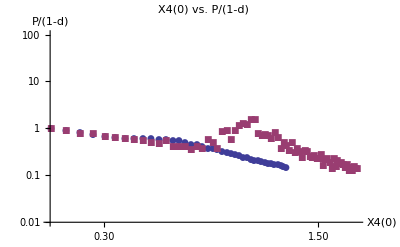

```mathematica
ListLogLogPlot[{data080,data098},PlotLabel->"X4(0) vs. P/(1-d)",AxesLabel->{"X4(0)","P/(1-d)"},PlotLegend->{"P=0.8","P=0.98"},PlotRange->{0.01,100},LegendPosition->{0.6,0},LegendShadow->None,LegendSize->{0.3,0.4},PlotMarkers->Automatic]
```

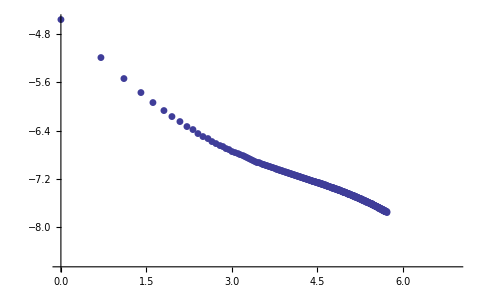

```mathematica
datax4001=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/X4tau001.txt",{Number,Number}];
ListLogLogPlot[datax4001,PlotLabel->"X4(t) vs. t (P = 0.98 & d = 0.01)",AxesLabel->{t,"X4(t)"},PlotRange->Full,PlotMarkers->Automatic]
```

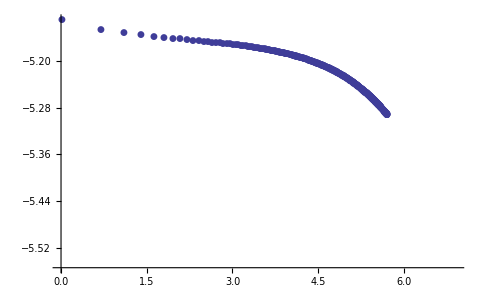

```mathematica
datax4003=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/X4tau003.txt",{Number,Number}];
ListLogLogPlot[datax4003,PlotLabel->"X4(t) vs. t (P = 0.98 & d = 0.03)",AxesLabel->{t,"X4(t)"}, PlotRange->Full,PlotMarkers->Automatic]
```